# Motion in a Potential Field - Feynman

### For a harmonic oscillator, the Lagrangian is:

```mathematica
L=m/2 x'[t]^2-m/2 ω^2 x[t]^2
```

-1/2 m ω^2 x[t]^2+1/2 m x'[t]^2

### Let’s test all the derivatives and see if we get the right results:

```mathematica
D[L,x[t]]
D[L,x'[t]]
```

-m ω^2 x[t]

m x'[t]

```mathematica
D[D[L,x'[t]],t]
```

m x''[t]

Yes we do!

### Find the equations of motion:

```mathematica
D[D[L,x'[t]],t]-D[L,x[t]]==0
```

m ω^2 x[t]+m x''[t]==0

Just one.

### Solve the equation of motion to get x(t):

```mathematica
sol=DSolve[{m ω^2 x[t]+m x''[t]==0,x[0]==xa,x[T]==xb},x,t]
```

{{x→Function[{t},xa Cos[t ω]-xa Cot[T ω] Sin[t ω]+xb Csc[T ω] Sin[t ω]]}}

### Trajectory Plots:

```mathematica
Clear[xa,xb,w,T,m];
```

```mathematica
par={xa->2,xb->4,ω->1,m->1,T->1}; 
par2={xa->0,xb->4,ω->1,m->1,T->1}; (* Different parameters)
```

```mathematica
f[t]=x[t]/.sol⟦1⟧/.par;
f2[t]=x[t]/.sol⟦1⟧/.par2;
```

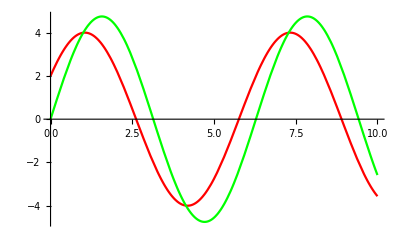

```mathematica
Plot[{f[t],f2[t]},{t,0,10},PlotStyle->{Red,Green}]
```

### Find the classical action:

```mathematica
G = L/.sol[[1]] (* Storing the Lagrangian with the solution plugged in *)
```

1/2 m (-xa ω Cos[t ω] Cot[T ω]+xb ω Cos[t ω] Csc[T ω]-xa ω Sin[t ω])^2-1/2 m ω^2 (xa Cos[t ω]-xa Cot[T ω] Sin[t ω]+xb Csc[T ω] Sin[t ω])^2

```mathematica
Scl=Integrate[G,{t,0,T}] (* Integrating the Lagrangian over time to get the classical action *)
```

1/2 m ω (-2 xa xb+(xa^2+xb^2) Cos[T ω]) Csc[T ω]